```mathematica
mub[s_]:=1307.5/(1+0.288*s)
```

```mathematica
mub[200]
```

22.3123

```mathematica
mub[62.4]
```

68.9203

```mathematica
mub[54.4]
```

78.4475

```mathematica
mub[39]
```

106.892

```mathematica
mub[27]
```

148.986

```mathematica
mub[19.6]
```

196.77

```mathematica
mub[14.5]
```

252.608

```mathematica
mub[11.5]
```

303.224

```mathematica
mub[7.7]
```

406.359

```mathematica
tc[s_]:=158.4/(1+Exp[2.60-Log[s]/0.45])
```

```mathematica
tc[200]
```

158.384

```mathematica
tc[62.4]
```

158.182

```mathematica
tc[54.4]
```

158.104

```mathematica
tc[39]
```

157.781

```mathematica
tc[27]
```

157.006

```mathematica
tc[19.6]
```

155.585

```mathematica
tc[14.5]
```

152.992

```mathematica
tc[11.5]
```

149.552

```mathematica
tc[7.7]
```

138.428

```mathematica
NumberForm[138.42845611642903,16]
```

138.428456116429

```mathematica
mub1={0.7,24,34,74,230,275,380,430,580}
```

{0.7,24,34,74,230,275,380,430,580}

```mathematica
Tf={156.5,156.5,151.8,140.4,128.8,124.2,113.9,107.3,80.9}
```

{156.5,156.5,151.8,140.4,128.8,124.2,113.9,107.3,80.9}

```mathematica
a=Transpose[{mub1,Tf}]
```

{{0.7,156.5},{24,156.5},{34,151.8},{74,140.4},{230,128.8},{275,124.2},{380,113.9},{430,107.3},{580,80.9}}

```mathematica
f=Interpolation[Transpose[{mub1,Tf}],Method->"Spline"]
```

InterpolatingFunction[{{0.7, 580.}}, <>]

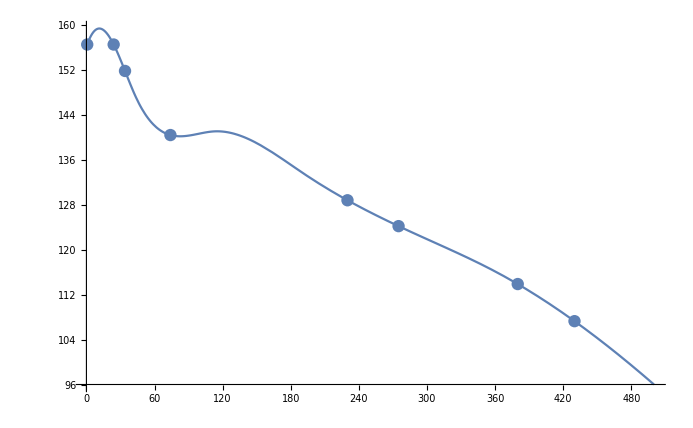

```mathematica
Show[Plot[f[x],{x,1,500}],ListPlot[a],ListPlot[f[x]]]
```

```mathematica
f[22.312286689419796]
f[68.92025807539851]
f[78.44748968033025]
f[106.89175931981688]
f[148.985870556062]
f[196.77040693474598]
f[252.60819165378675]
f[303.22356215213364]
f[406.358776727996]
```

157.147

140.787

140.227

140.928

139.075

132.829

126.395

121.593

110.586

157.147